# On Functional Iteration and Roots

By Bertie Bennet, Christopher Gilbert, and Gregory Roudenko

## Introduction

## Abstract

This project explores non-integer iteration of functions of one or more variables. We present algebraic solutions to roots of some generalized functions, and detail various numerical and algebraic root-finding algorithms.

## Introduction

### Basic Definitions

Composition, denoted with the symbol ◦, involves inputting one function’s output into another’s input. For example, (f ◦ g)(x) is equivalent to f(g(x)). When the same function is composed with itself multiple times, (e.g. f(f(f(x)))) it is said to be nested.

Let (f ◦ f ◦ f...)_n where n ∈ ℕ (i.e. nesting) be denoted f^n, where ◦ denotes composition. f^n may be  called the nth functional exponent of f.

#### Implementation

Helper function for overloading:

```mathematica
FunctionQ[f_]:=Head[f]===Function||!((Information[f, "Definitions"][[0]]===Information)||Information[f, "Definitions"]===None)||(Quiet[Context[f],Context::ssle]==="System`"&&DownValues[f]==={})
```

Overloading Composition (i.e. @* operator) to do repeated composition

```mathematica
Unprotect[Composition];
Composition[f_?FunctionQ, n_Integer?Positive]:=Nest[f@*#&,f, n-1]
Composition[f_?FunctionQ, 0]:=Composition@@{};
Protect[Composition];
```

Symbolic Example

```mathematica
f[x_]:=x^2
f@*4
```

f@*f@*f@*f

Application Examples

```mathematica
(f@*4)[x]
```

x^16

```mathematica
(f@*0)[x]
```

x

### Properties

Composition of the same nested function is additive, so f^n ◦ f^m = f^(n+m).
Nesting a nested function is multiplicative, so (f^n)^m=f^nm.
In these ways, functional exponentiation and composition have similar algebraic properties to exponentiation, such as the rules that e^a e^b=e^(a+b) and (e^a)^b=e^(a×b).

### Generalized Nesting

#### Integers

Although nesting so far has only been defined for the natural numbers, it can be extended based on the properties above.
If we define f^0(x)=x and f^-n=(f^-1)^n (where f^-1 is the inverse function of f), then the above properties of composition and nesting now hold for integer nestings.

E.g. for some function f with an inverse f^-1:
By the definition of the inverse function, (f^1◦ f^-1)(x)=x
Equivalently, with our definitions and properties, (f^1◦ f^-1)(x)=f^(1-1)(x)=f^0(x)=x

#### Inverses and Rationals

In the same way that composition being additive leads to a generalization to the integers, nesting being multiplicative leads to a generalization to the rationals.
Let the m-th functional root be denoted f^(1/m). This function has the property that nesting it m times will result in the original function f, because
(f^(1/m))^m=f^(m/m)=f^1

E.g. f^(1/2)◦ f^(1/2)=f^(1/2 + 1/2)=f^1
In other words, f’s square root g must satisfy g(g(x)) = f(x)

By the same logic, let the functional exponent f^(n/m) be defined as the m-th root of f^n, or, equivalently, the nth nesting of the m-th root of f.

#### Reals

For some w ∈ ℝ, define f^w(x) =lim_(i->∞) (f^(⌊2^i w⌋/⌊2^i⌋)(x)). This is simply the limit of a rational approximation of w.

#### Complexes

Occasionally, it may be even possible to generalize functional iteration to complex. That is, the i-th exponent of f, f^𝕚, must satisfy the property that (f^𝕚)^𝕚=f^(𝕚^2)=f^-1.

#### Goal of the Project

In general, the goal of the project will be finding and exploring solutions or approximations of non-Integer functional exponents.

## Basic Examples of Explicit Solutions

Beyond trivial examples where f(f(x)) = f(x) (e.g. f(x) = a, f(x) = x, f(x) = Ramp(x)), here we will explore algebraic solutions to simple functional exponents.

### Helper Functions

Generates the coefficients of the powers of x. Non-power terms are included as the values of _. For example, f(x) =a_0+a_1 x+a_2 x^2... becomes {0->a_0, 1->a_1..., _->0}:

```mathematica
coefList[symb_, {eMin_:0, eMax_:1}, var_:x, includeRemainder_:True]:=Module[{coefs},
coefs=Table[e->Plus@@(If[(#/.var->temp)===#, #,0]&/@(List@@Expand[symb var^-e])), {e, eMin, eMax}];
If[includeRemainder,Append[coefs, _->Expand[symb-(Values[coefs].(var^(Range[Length[coefs]]-1)))]],coefs]]
```

Example:

```mathematica
coefList[2+c+s x+s x^3+Log[x],{0,3},x]
```

{0→2+c,1→s,2→0,3→s,_→Log[x]}

## Affine Functions

An affine function is a function which can be written f(x) = a + b x. Using Solve[], one can find a simple, affine solution to the functional m-th root of f.
This method only works if the structure of f^(1/2) is known. That is, the affine nature of f^(1/2) can be guessed, and because an exact solution exists, it can be seen that this guess is true. Such a structure becomes more difficult to find as a function becomes more complex, and is the main challenge in finding exact solutions to most functions.

Set up affine function form (and use 1/7th as the iterate):

```mathematica
m=7;
f[x_]:=a+b x
fRoot[x_]:=r+s x
```

Find (f^(1/m))^m(x). Then, solve for the coefficients in f^(1/m):

```mathematica
fRootNested=(fRoot@*m)[x]//PowerExpand//Expand
```

r+r s+r s^2+r s^3+r s^4+r s^5+r s^6+s^7 x

```mathematica
fCoefs=coefList[f[x], {0, 1}];
fRootCoefs=coefList[fRoot[x],{0, 1}];
fRootNestedCoefs=coefList[fRootNested,{0, 1}];
```

Solve for the coefficients of (f^(1/m)):

```mathematica
(fullSolution=Solve[
And@@Thread[#1==#2&[Values[fCoefs], Values[fRootNestedCoefs]]],
Values[fRootCoefs[[;;-2]]]
])//Column
```

{r→(-a+a b^(1/7))/(-1+b),s→b^(1/7)}
{r→(-a-(-1)^(1/7) a b^(1/7))/(-1+b),s→-(-1)^(1/7) b^(1/7)}
{r→(-a+(-1)^(2/7) a b^(1/7))/(-1+b),s→(-1)^(2/7) b^(1/7)}
{r→(-a-(-1)^(3/7) a b^(1/7))/(-1+b),s→-(-1)^(3/7) b^(1/7)}
{r→(-a+(-1)^(4/7) a b^(1/7))/(-1+b),s→(-1)^(4/7) b^(1/7)}
{r→(-a-(-1)^(5/7) a b^(1/7))/(-1+b),s→-(-1)^(5/7) b^(1/7)}
{r→(-a+(-1)^(6/7) a b^(1/7))/(-1+b),s→(-1)^(6/7) b^(1/7)}

Return the only real solution:

```mathematica
sol=Normal[Association[Join[{r->0, s->0},First[fullSolution]]]]
```

{r→(-a+a b^(1/7))/(-1+b),s→b^(1/7)}

Based on the above computation, a general m-th root formula is given by:  f^(1/m)(x)=a(b^(1/m) -1)/(b-1)+b^(1/m)x
This can be extended to a general exponentiation formula for rationals,  reals, and complexes:  f^z(x)=a(b^z -1)/(b-1)+b^z x

Plot any affine function with a z-th iterate:

```mathematica
Manipulate[Labeled[Plot[{a+b x, (a(b^z-1))/(b-1)+b^z x}, {x, -10, 10}, PlotRange->{-30, 30},PlotLegends->{"TraditionalForm`f(x) = a + b\ x", "f^z(x)"}],"Plot of affine f and f^z"],{z, -2, 2},{a, -2, 2},{b, 2^-16, 2}]
```

Plot any affine function for any real z:

```mathematica
Manipulate[Labeled[ Plot3D[(-a+a b^z)/(-1+b)+b^z x, {x, -2, 2}, {z, -2, 2}, AxesLabel->{"x", "z", "f"}],"Plot of f where TraditionalForm`f(x) = a + b\ x"],{a, -2, 2}, {b,2^-16, 2}]
```

## Power Functions / Monomials

One of the most useful ways of finding roots of functions is to first iterate them, then look for structure or formulas within the nested function which can be extended to noninteger nesting (i.e. root finding). Such a method was employed in order to find the general formula for functions of the form f(x)=a*x^b.

f^1(x)=a*x^b

f^2(x)=a*(a*x^b)^b=a^(1+b)*x^(b^2)

f^3(x)=a*(a*(a*x^b)^b)^b=a^(1+b+b^2)*x^(b^3)

f^4(x)=a*(a*(a*(a*x^b)^b)^b)^b=a^(1+b+b^2+b^3)*x^(b^4)

The pattern emerges that the nth nest of f is a^(b^0+b^1+...+b^(n-1))*x^(b^n)
Because that sum of powers of b is a geometric sequence, it can be replaced with the formula for a geometric sequence, and by this method the final formula is obtained:
f^n(x)=a^((b^n-1)/(b-1))x^(b^n)
Although this formula was defined in terms of discrete sums, by using the geometric sum formula, it may be generalized to all complex numbers:
f^z(x)=a^((b^z-1)/(b-1))x^(b^z)

Generalized monomial:

```mathematica
monomialRoot[a_,b_,x_, z_]:=a^((b^z-1)/(b-1))*x^(b^z)
```

Plot of x^2 and its iterates:

```mathematica
Manipulate[Labeled[Plot[{1*x^2,monomialRoot[1, 2, x, z]}, {x, 0, 1.2}, PlotRange->{-0.1, 1.54}, PlotLegends->{"TraditionalForm`f", "f^z(x)"}],"Plot of f(x)=x^2 and it's zth exponent"],{z, -3, 3, 0.1}, SaveDefinitions->True]
```

Plot of complex iterates of x^2:

```mathematica
Manipulate[Labeled[Quiet[ComplexPlot[monomialRoot[1, 2, xRe+I*xIm, z], {z, -10-10I, 10+10I}], General::munfl], "Plot of f^z with respect to z"], {xRe, -10, 10}, {xIm, -10, 10}, SaveDefinitions->True]
```

## Inverse Function Composition

If one compares the formulas for the iterate of a monomial and the iterate of an affine function, many similarities may become apparent: the coefficients in one are closely related to the exponents of the other, and both share a similar structure. When given a monomial function M, if you compute ln(M(e^x)), you will see that it is an affine function. Let A(x)=ln(M(e^x)). If you find the z-th functional exponent of both M and A, you will see that same relationship: A^z(x)=ln(f^z(e^x)).

Although easiest to identify in the case of affine and monomial, this can be generalized to all functions, and to all function-inverse function pairs:
If g(x)=j^-1(f(j(x))), then g^z(x)=j^-1(f^z(j(x))), provided j^-1 and j are defined over the required domains.

For a rational exponent z, this statement is fairly easy to prove. For example, if z=1/2:

Let g(x)=j^-1(f(j(x)))

g^(1/2)(g^(1/2)(x))=j^-1(f(j(x)))

g^(1/2)(g^(1/2)(x))=j^-1(f^(1/2)(f^(1/2)(j(x))))

g^(1/2)(g^(1/2)(x))=j^-1(f^(1/2)(j(j^-1(f^(1/2)(j(x))))))

g^(1/2)(x)=j^-1(f^(1/2)(j(x)))

And so we arrive at the above formula. As this method of proof can be generalized to all rational exponents, it can be extended to the reals and complexes through a similar method as given above for the extending of functional nesting into functional exponentiation.

## Formulas found by this technique

If  the exponent of a function f is known, by this technique, the exponent of any function of the form j^-1(f(j(x))) may be found (given some domain constraints on j^-1 and j).

### Cos(M(ArcCos(x)))

For example, because the formula for the iterate of a monomial M is known, one can find the iterate of a cos(M(arccos(x))):

M(x)=a*x^b
f(x)=cos(a*(arccos(x))^b)

M^z(x)=a^((b^z-1)/(b-1))x^(b^z)
f^z(x)=cos(a^((b^z-1)/(b-1))(arccos(x))^(b^z))

```mathematica
Manipulate[Labeled[Quiet[Plot[Cos[a^((b^(1/2)-1)/(b-1))ArcCos[x]^(b^(1/2))], {x, -1, 1}, PlotRange->{{-1,1}, {-1, 1}}], General::munfl], "Plot of f^(1/2)(x) where f(x)=cos(a arccos(x)^b)"], {a,3, 10}, {b, 3, 10}]
```

### Tan(M(ArcTan(x)))

ArcCos has a bounded range [-1, 1], so a different choice of j may lead to more interesting results. For example, tan(M(arctan(x))) for some monomial M:

M(x)=a*x^b
f(x)=tan(a*(arctan(x))^b)

M^z(x)=a^((b^z-1)/(b-1))x^(b^z)
f^z(x)=tan(a^((b^z-1)/(b-1))(arctan(x))^(b^z))

```mathematica
Manipulate[Labeled[Quiet[Plot[Tan[a^((b^z-1)/(b-1))ArcTan[x]^(b^z)], {x, -10, 10}, PlotRange->{All, {-Pi/2, Pi/2}}], General::munfl], "Plot of f^z(x) where f(x)=tan(a arctan(x)^b)"], {a,3, 10}, {b, 3, 10}, {z, 0, 3}]
```

### Ln(Sin(Exp(x)))

Although an exact formula for sin^(1/2) is not known, an approximation can be found through techniques shown later in this computational essay, of which one will be used here.

f(x)=ln(sin(exp(x)))

f^(1/2)(x)=ln(sin^(1/2)(exp(x)))

```mathematica
(* A simple approximation of Sin^(1/2). Although we explored using approximations of this form, they did not prove generally useful except for basic examples such as this. *)
rootSinBasicApprox[theta_]:=Sin[theta]+Sin[Sin[theta]]-Sin[Sin[Sin[theta]]]
```

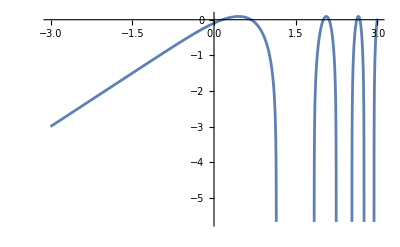
-Graphics-Plot of f^(1/2)(x) where f(x)=ln(sin(e^x)))

```mathematica
Labeled[Quiet[Plot[Log[rootSinBasicApprox[Exp[x]]], {x, -3, 3}], General::munfl], "Plot of f^(1/2)(x) where f(x)=ln(sin(e^x)))"]
```

And indeed, if this root is iterated with itself, it gives an approximation for f:

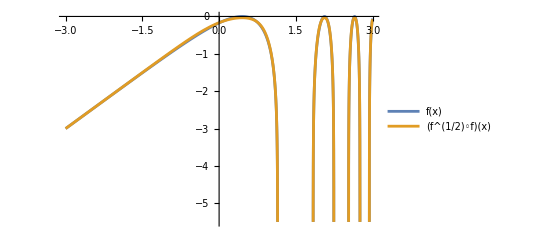
-Graphics-Plot of f(x) and it's approximation where f(x)=cos(a arccos(x)^b)

```mathematica
Labeled[Quiet[Plot[{Log[Sin[Exp[x]]],Log[rootSinBasicApprox[Exp[Log[rootSinBasicApprox[Exp[x]]]]]]}, {x, -3, 3}, PlotLegends->{"f(x)", "(f^(1/2)◦f)(x)"}], General::munfl], "Plot of f(x) and it's approximation where f(x)=cos(a arccos(x)^b)"]
```

## Numerical Methods

As many functional roots are very difficult to find, and in many cases (such as polynomials on the full complex plane), are proven to have no solutions, this paper now examines methods for finding functional iterates (but mainly functional square roots) using numerical methods.

## Method 1: Recursive Function Values

#### Helper Functions

As many operations in this notebook take a very long time to run, this function gives an progress indicator for them:

```mathematica
progressMap[func_,l_List, message_:"Complete"]:=Module[{progress=PrintTemporary["0% "<>message]}, Table[NotebookDelete[progress];progress=PrintTemporary[ToString[Round[100*i/Length[l]]]<>"% "<>message]; func[l[[i]]],{i, Length[l]}]]
```

Example

```mathematica
progressMap[
(* A difficult function *) 
Pause[0.01]&, 

Range[0, 100]
];
```

Makes a linear spline between points (i.e. connects them with straight lines), and extends the domain using the last two points on either end.

```mathematica
LinearSpline[points_][x_]:=Module[{p, m, xs,table},
p=Sort[points,#1[[1]]<#2[[1]]&];
m=If[#1==0,2^16,(#2/#1)]&@@@(Drop[p,1]-Drop[p, -1]);
table=Table[{Drop[p,-1][[i,1]]<=x<Drop[p, 1][[i,1]],m[[i]]*(x-Drop[p,1][[i,1]])+Drop[p,1][[i,2]]},{i,Length[p]-1}];
table=Flatten@Join[{x<p[[1,1]], table[[1,2]]}, table, {x>=p[[-1,1]], table[[-1,2]]}];
Which@@table
]
```

Example

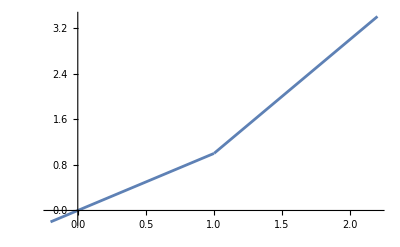

```mathematica
ls=LinearSpline[{{0, 0}, {1, 1}, {2, 3}}];
Plot[ls[x], {x, -0.2, 2.2}]
```

Returns the loss of an approximation when nested

```mathematica
NestedLoss[fOriginal_, g_, rmin_, rmax_]:=Quiet[NIntegrate[(f[x]-g[g[x]])^2, {x, rmin, rmax}], NIntegrate::ncvb]
```

### Input

Input a function and a finite range over which the solution will be found. The step size indicates the distance between the points where error is calculated.

```mathematica
f[x_]:=Sin[x]+LogisticSigmoid[x];
originalRange={-2*Pi,2*Pi,0.3};
range=originalRange;
```

Here is a plot of the inputted function over the range:

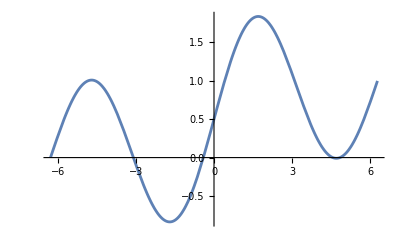

```mathematica
pRange=AbsoluteOptions[Plot[f[x], {x, range[[1]], range[[2]]}, ImageSize->Medium],PlotRange][[1,2]];
pRange[[2,1]]=Min[0,pRange[[2,1]]]; (* Set the plotting range manually *)

Plot[f[x],{x, range[[1]], range[[2]]}, PlotRange->pRange]
```

### Explanation

We are trying to solve the equation g(g(x)) = f(x) for all x.
Given an initial x, xi, we can make a guess as to the value of g:
g(xi) = w
Because we know that g(g(x)) = f(x), then g(g(xi)) = f(xi), and since g(xi) = w, then:
g(w) = f(xi)
This gives a second value of g. For a third, we can repeat the same thing. g(g(x)) = f(x), so g(g(w)) = f(w), and since g(w) = f(xi):
g(f(xi)) = f(w)
If you continue this, you get as many points as you want that will all lie on the g, assuming that g(xi) = w. By searching over all xi and all w, we can find the solution which minimizes the squared difference between a linear spline of the approximating points and the original function.

This is a function which more efficiently implements the process described above:

```mathematica
approximatingPoints[xii_,w_,n_:20]:=Riffle[Transpose[{NestList[f, xii, n], NestList[f, w, n]}],Transpose[{NestList[f, w, n], NestList[f, f[xii], n]}]]
```

FInally, here are more helper functions relating to it, which are fairly self-explanatory.

```mathematica
approxFunc[xii_, w_]:=LinearSpline[approximatingPoints[xii, w]]
error[af_]:=Quiet[Sum[(af[af[x]]-f[x])^2, {x, range[[1]], range[[2]], range[[3]]}]*range[[3]],General::munfl]
errorFunc[xii_, w_]:=error[approxFunc[xii,w]]
```

### Search

For every xii and w, the Search[] function checks the error of it, setting minP to be the values of xii and w which minimize error, and returning that minimum error. By then subdividing the region around minP, a better and better solution can be found. As the first iteration is the biggest search (in order to minimize the effect of local minima), it takes much longer than all other iterations.

```mathematica
(* Tweak the last value of each of these for faster first-step evaluation times. *)
(* Localization is not used so that search can be run multiple times to improve accuracy. *)
xiiRange=range;wRange=range; 

search[anything___]:=(
points=ParallelTable[errorFunc[xii, w],{xii, xiiRange[[1]],  xiiRange[[2]],  xiiRange[[3]]}, {w, wRange[[1]],  wRange[[2]],  wRange[[3]]}];
minI=First[Position[points,Min[points],2]];
minP={xiiRange[[1]]+minI[[1]]xiiRange[[3]], wRange[[1]]+minI[[2]]wRange[[3]]};
minV=errorFunc@@minP;

xiiRange={minP[[1]]-xiiRange[[3]], minP[[1]]+xiiRange[[3]], 0.5xiiRange[[3]]};
wRange={minP[[2]]-wRange[[3]], minP[[2]]+ wRange[[3]], 0.5wRange[[3]]};

minV
);
```

```mathematica
PrintTemporary["The first step takes way longer than future steps"];
progressMap[search,Range[20]]
```

{145646.,553.154,15.6083,4.68805,3.48817,3.18523,3.07492,3.02761,3.00568,2.99513,2.98995,2.98739,2.98611,2.98547,2.98515,2.985,2.98492,2.98488,2.98486,2.98485}

### Output

Based on the search, here is the best function found so far:

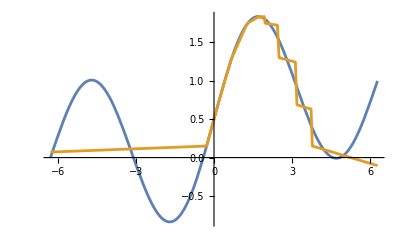

```mathematica
aFunc= approxFunc@@minP;
Plot[{f[x], aFunc[aFunc[x]]}, {x, range[[1]], range[[2]]}, PlotRange->pRange]
```

And here are the xii and w values, and the error which were achieved:

```mathematica
minP
minV
```

{4.21682,-0.283185}

2.98485

### Analysis

Although this method does find some points on the function, and the general “shape” of it for positive numbers (especially small positive numbers), it has a final total error (i.e. the area under the curve of the squared difference between the function and it’s approximation) of:

```mathematica
NestedLoss[f, aFunc, range[[1]], range[[2]]]
```

3.1185

## Method 2: Simultaneous function value optimization

### Explanation

Instead of being smart about nesting functions with a single initial guess, this method tries to determine the whole function at once in order to move the values closer to what is needed. It is extremely susceptible to local minima, but it can often do a much better job of optimizing simpler functions, such as sine or some polynomials.

First, take a guess at a functional root g. I’ve used the g from method 1 here, but you could probably use almost anything. In fact, one possible route for further exploration is to randomize the initial function g, then search from there. In this way, some local minima for the optimization function may be avoided.
Next, find the differences between that and the original function:
delta(x) = f(x) - g(g(x))

Finally, simply add the delta to update g:
new_g(x) = g(x) + temperature * delta(x)

For some points, g(x) will not be affected much, but g(g(x)) will be moved closer to f. In this case, g will be positively affected. For other points, it may shoot off to infinity or become discontinuous, so there is no real guarantee that this will work.

### Implementation

First, this code represents both the original function and the approximation as a set of points, with xVals being the x values of the points, fVals being the corresponding y values of the original function, and aVals being the approximated y values. Using a linear spline, it approximates the corresponding functions from these lists of points.

```mathematica
range[[3]]=originalRange[[3]]/5;  (* Increase resolution, as this method is faster and can handle more points *)

aFunc= approxFunc@@minP;  (* Optimal function from the previous method *)
xVals=Range@@range; 
fVals=f/@xVals;
aVals=aFunc[aFunc[#]]&/@xVals;

(* Generates the interpolating function from a list of y values *)
funcFromVals[vals_]:=LinearSpline[Transpose[{xVals,  vals}]]
```

Here are plots of the interpolated values for the original function and the function from method 1:

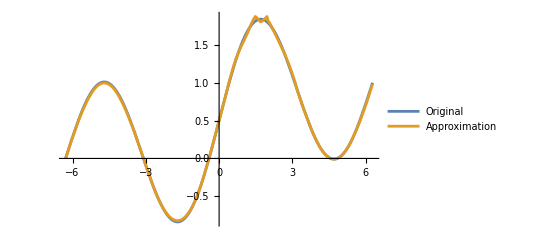

```mathematica
PlotVals[vals_]:=Show[{ListPlot[Transpose[{xVals, vals}],PlotRange->pRange],  Plot[funcFromVals[vals][x], {x, range[[1]], range[[2]]},PlotRange->pRange]}]
Plot[{f[x], aFunc[aFunc[x]]}, {x, range[[1]], range[[2]]}, PlotLegends->{"Original", "Approximation"}]
```

### Optimization

This repeatedly applies the method described to optimize the function.

```mathematica
aValsHist={aVals};
progressMap[
(aFunc=funcFromVals[aVals];
aVals=aVals+0.3*(fVals-ParallelMap[aFunc[aFunc[#]]&,xVals]);
AppendTo[aValsHist, aVals];)&,Range[50] , "Optimized"];

(* Find the optimization which actually minimized error *)
bestVals=aValsHist[[First[PositionSmallest[ParallelMap[error[funcFromVals[#]]&,aValsHist]]]]];
aFunc=funcFromVals[bestVals];
```

Plot the progress made so far:

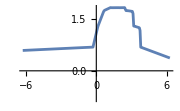
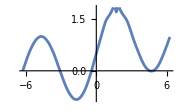
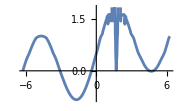
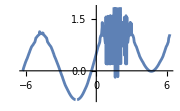
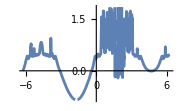

```mathematica
ParallelMap[With[{aFunc=funcFromVals[aValsHist[[#]]]},Plot[aFunc[aFunc[x]], {x, range[[1]], range[[2]]}, ImageSize->Small, PlotRange->pRange]]&, Round/@Subdivide[1, Length[aValsHist], 4]]
```

You can see that in the case of the example function, this method does eventually diverge. However, before then, it does find a quite close solution.

### Output

Here is the output of the optimization:

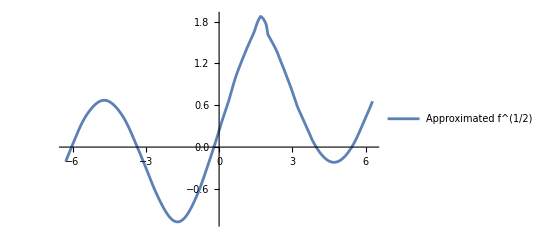

```mathematica
Plot[aFunc[x], {x, range[[1]], range[[2]]}, PlotLegends->{"Approximated f^(1/2)"}]
```

And the nested approximation compared to the original:

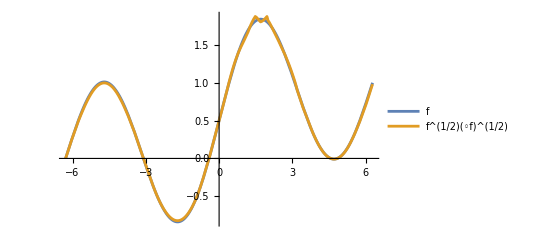

```mathematica
Plot[{f[x], aFunc[aFunc[x]]}, {x, range[[1]], range[[2]]}, PlotLegends->{"f", "f^(1/2)(◦f)^(1/2)"}]
```

### Analysis

This approximation already looks much more promising, and indeed, when the loss is found, it comes out to be much smaller, though with some improvement still possible

```mathematica
NestedLoss[f, aFunc, range[[1]], range[[2]]]
```

0.00242972

## Method 3: Genetic Algorithm of Fourier and Taylor Series Approximations

### Built-In Optimization of Fourier Series

For some functions like Sin and Cos, fourier series approximations of their roots converge very quickly, and so a good approximation can be found with relatively little computational power. For example, a 9th degree summation of sines can be minimized to a squared error of less than 10^-7:

```mathematica
n=9;  (* Number of Sine Terms *)
Clear[a];  (* Symboilic vector of coefficients *)

sol=Quiet[NMinimize[
Quiet[NIntegrate[
(Sin[x]-Sum[a[i]*Sin[i Sum[a[j]*Sin[j x],{j,n}]],{i,n}])^2,{x,-2Pi,2Pi}
]],
Table[a[i],{i,n}]
]];

approx[x_]:=Values[Last[sol]].Table[Sin[i x],{i,n}]
```

Error Value:

3.83823×10^-8

Sin Coefficients:

{a[1]→1.09381,a[2]→-6.70455×10^-8,a[3]→-0.038811,a[4]→1.18527×10^-7,a[5]→0.00582721,a[6]→-5.7619×10^-8,a[7]→-0.00119246,a[8]→-4.52284×10^-7,a[9]→0.000241406}

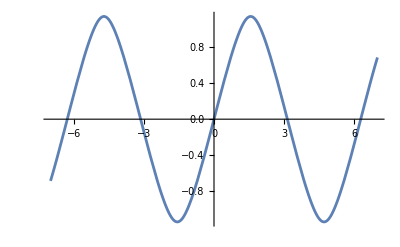
-Graphics-Fourier Series Sin^(1/2) Approximation

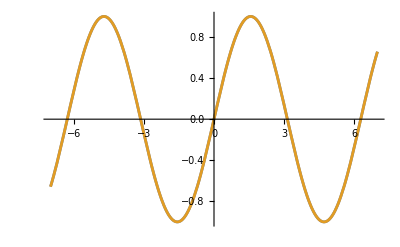
-Graphics-Sin and Sin^(1/2)(◦Sin)^(1/2)

```mathematica
"Error Value:"
sol[[1]]

"Sin Coefficients:"
sol[[2]]

Labeled[Plot[approx[x], {x, -7,7}], "Fourier Series Sin^(1/2) Approximation"]
Labeled[Plot[{Sin[x], approx[approx[x]]}, {x, -7,7}], "Sin and Sin^(1/2)(◦Sin)^(1/2)"]
```

However, this method is quite slow, and scales up exponentially with more terms. (Although using a different Method parameter for NMinimize may reduce this).

### Rust-Based Approximations

Because of the speed concerns, and also for greater flexibility in the types of series-based approximations that we wanted to test, we wrote a genetic algorithm in the low-level programming language Rust, which can approximate functions by means of Fourier series, and Taylor series, and Linear splines.

#### Rust Code

This code can also be found at https://github.com/Christopherfrommaine/WELP/tree/main/Functional%20Iterates%20Notebooks/Christopher%20Exploration/RUST-genetic-sine-solver.

main.rs

use std::fmt;
use cgrustplot::plots::func_plot::function_plot;  // A custom plotting library, for plotting the output
use rand::distributions::{Uniform, Distribution};  // For random mutations
use rayon::prelude::*;  // For parallelization

// // Mathematical Helpers
const PI: f64 = std::f64::consts::PI;
const RANGE: (f64, f64) = (-2. * PI, 2. * PI); // Range over which to evaluate the function

fn factorial(num: usize) -> usize {
    let mut o = 1;
    for i in 1..=num { o *= i; }
    o
}

fn rand_vec(len: usize, range: (f64, f64)) -> Vec<f64> {
    let mut rng = rand::thread_rng();
    let dist = Uniform::new(range.0, range.1);

    (0..len)
        .map(|_| dist.sample(&mut rng))
        .collect()
}

// Generate a function from a fourier series
fn fourier(coefs: &Vec<f64>) -> impl Fn(f64) -> f64 {
    let c = coefs.clone();
    
    move |x: f64| c
        .iter()
        .enumerate()
        .map(|(i, c)|
            c * (i as f64 * x).sin()
        ).sum::<f64>()
}

// Generate a function from a fourier series
fn cosine_fourier(coefs: &Vec<f64>) -> impl Fn(f64) -> f64 {
    let c = coefs.clone();
    
    move |x: f64| c
        .iter()
        .enumerate()
        .map(|(i, c)|
            c * (i as f64 * x).cos()
        ).sum::<f64>()
}

// Generate a function from a taylor series
fn taylor(coefs: &Vec<f64>) -> impl Fn(f64) -> f64 {
    let c = coefs.clone();

    move |x: f64| c
        .iter()
        .enumerate()
        .map(|(i, c)|
            c * x.powi(i as i32) / factorial(i) as f64
        ).sum::<f64>()
}

// Generate a function from a linear spline
fn linear(coefs: &Vec<f64>) -> impl Fn(f64) -> f64 {
    let c = coefs.clone();

    let n = c.len();
    let dx = (RANGE.1 - RANGE.0) / (n - 1) as f64;

    move |x: f64| {
        if x < RANGE.0 || x > RANGE.1 {
            0.
        } else {
            let left = ((x - RANGE.0) / dx).floor() as usize;
            let right = ((x - RANGE.0) / dx).ceil() as usize;

            if left == right {
                return c[left]
            }
            
            let weight = (x - (RANGE.0 + left as f64 * dx)) / dx;

            (1. - weight) * c[left] + weight * c[right]
        }
    }
}

// Use a reiman sum to integrate the loss of a function
fn loss<F: Fn(f64) -> f64, G: Fn(f64) -> f64>(f: F, g: G) -> f64 {
    const RESOLUTION: f64 = 0.01;
    RESOLUTION * (((RANGE.0 / RESOLUTION) as i32)..(RANGE.1 / RESOLUTION) as i32)
    .map(|i| i as f64 * RESOLUTION)
    .map(|x| (g(x) - f(x)).powi(2))
    .sum::<f64>()
}

// Approximation definitions
#[derive(Debug, Clone)]
struct Approx {
    coefs: Vec<f64>,
    loss: Option<f64>,
    typ: char
}

impl fmt::Display for Approx {
    fn fmt(&self, f: &mut fmt::Formatter<'_>) -> fmt::Result {
        // Format the coefficients to be able to be copied into wolfram
        let formatted_coefs_original: Vec<String> = self.coefs.iter().map(|i| format!("{:.16}, ", i)).collect();
        let mut formatted_coefs = vec![String::from("{")];
        formatted_coefs.extend(formatted_coefs_original);
        let fcl = formatted_coefs.len() - 1;
        formatted_coefs[fcl] = formatted_coefs[fcl][..(formatted_coefs[fcl].len()-2)].to_string();
        formatted_coefs.push(String::from("}"));
        let coefs_string = formatted_coefs.join("");
        write!(f, "\nBest Coefficients: \n{coefs_string}")
    }
}

impl Approx {
    fn new(coefs: Vec<f64>, typ: char) -> Self {
        Self {
            coefs,
            loss: None,
            typ,
        }
    }

    fn as_func(&self) -> Box<dyn Fn(f64) -> f64> {
        match self.typ {
            'f' => Box::new(fourier(&self.coefs)),
            't' => Box::new(taylor(&self.coefs)),
            'l' => Box::new(linear(&self.coefs)),
            'c' => Box::new(cosine_fourier(&self.coefs)),
            _ => Box::new(|x: f64| x),
        }
        
    }

    fn eval(&mut self, f: impl Fn(f64) -> f64) -> &Self {
        let func = self.as_func();

        self.loss = Some(loss(f, |x| func(func(x))));
        self

    }

    fn mutate(&self, temp: f64) -> Self {
        let adj: Vec<f64> = rand_vec(self.coefs.len(), (-temp, temp));
        let adj_coef: Vec<f64> = self.coefs
            .iter()
            .zip(
                adj.iter()
            )
            .map(|(a, b)| a + b)
            .collect();
        
        Self::new(adj_coef, self.typ.clone())
    }

    fn plot(&self) {
        // Use cgrustplot to plot the aprpoximation in the console
        let func = self.as_func();
        function_plot(func)
            .set_title(String::from("- Root Approximation - - -"))
            .set_domain(RANGE)
            .print();

        let func = self.as_func();
        let nested_func = move |x| func(func(x));
        function_plot(nested_func)
            .set_title(String::from("- Nested Root Approximation - - -"))
            .set_domain(RANGE)
            .print();
    }
}

fn eval_all<F: Fn(f64) -> f64 + Sized + Clone + std::marker::Sync>(v: &mut Vec<Approx>, f: &Box<F>) {
    v
    .par_iter_mut()
    .for_each(|ta|
        {ta.eval(f.clone());}
    );
}

fn sort_approx<F: Fn(f64) -> f64 + Sized + Clone + std::marker::Sync>(v: &mut Vec<Approx>, f: &Box<F>) {
    eval_all(v, f);

    v.sort_by(|a, b| a.loss.unwrap().partial_cmp(&b.loss.unwrap()).unwrap_or(std::cmp::Ordering::Equal))
}

fn random_approximations(num: usize, range: (f64, f64), coef_number: usize, typ: char) -> Vec<Approx> {
    (0..num).map(|_|
        Approx::new(rand_vec(coef_number, range), typ)
    )
    .collect()
}

/// Increases the number of fourier terms in a list of approximations
fn elongate(v: Vec<Approx>, n: usize, typ: char) -> Vec<Approx> {
    v
    .into_iter()
    .map(|ta| {
        let mut new_coefs = ta.coefs;
        new_coefs.extend((0..n).map(|_| 0.));
        Approx::new(new_coefs, typ)
    }).collect()
}

fn avg_loss(v: &Vec<Approx>) -> f64 {
    v.iter().map(|ta| ta.loss.unwrap_or(0.)).sum::<f64>() / v.len() as f64
}

fn genetic_optimize<F>(f: &Box<F>, approxes: Vec<Approx>, gens: u32, max_num: usize, min_num: usize) -> Vec<Approx>
where 
    F: Fn(f64) -> f64 + Sized + Clone + std::marker::Sync
{

    let mut v = approxes;

    // Zero mutation, for faster convergence of taylor series
    v.push(Approx::new(v[0].coefs.iter().map(|_| 0.).collect::<Vec<f64>>(), v[0].typ));

    let mut prev_loss: f64;
    let mut min_loss = f64::INFINITY;
    let mut t = 1.;

    for i in 0..gens {
        let debug_string = format!("\rGen {:03}/{gens} | temp: {t:.6} | Min Loss {min_loss:.4} | Average Loss: {:.4}    ", i + 1, avg_loss(&v));
        let debug_string2 = &debug_string[..(if debug_string.len() > 80 {80} else {debug_string.len()})];
        print!("{debug_string2}");
        
        // Generate mutations
        while v.len() < max_num {
            let extras: Vec<Approx> = v.par_iter().map(|ta| ta.mutate(t)).collect();
            v.extend(extras);
        }

        // Sort by loss
        sort_approx(&mut v, f);

        // Select the best
        v = v[..min_num].to_vec();

        prev_loss = min_loss;
        min_loss = v[0].loss.unwrap_or(0.);

        // Adjust temperature to allow for fast descent (0.1% improvement per step) while not staying at 0. 
        if min_loss == prev_loss {
            t *= 0.5;
        } else if min_loss / prev_loss > 0.99 {
            t *= 2.;
        }
        t *= 1.05;
    }

    print!("\n");

    v
}

// // EXAMPLES:
#[allow(dead_code)]
fn taylor_example<F>(f: &Box<F>) -> Approx
where 
    F: Fn(f64) -> f64 + Sized + Clone + std::marker::Sync
{
    let approx_type = 't';

    // Original random input
    let mut out: Vec<Approx> = random_approximations(2048, (-0.1, 0.1), 8, approx_type);
    
    // Optimize with different numbers of surviving approximations
    out = genetic_optimize(f, out, 500, 2048, 256);
    out = genetic_optimize(f, out, 2000, 256, 64);
    out = elongate(out, 8, approx_type);
    out = genetic_optimize(f, out, 500, 64, 16);
    out = genetic_optimize(f, out, 2000, 32, 8);
    
    // Find best approximation, output it
    sort_approx(&mut out, f);
    let best = (&out[0]).clone();
    println!("Best Coefficients: {best}");
    best.plot();
    best
}

#[allow(dead_code)]
fn fourier_example<F>(f: &Box<F>) -> Approx
where 
    F: Fn(f64) -> f64 + Sized + Clone + std::marker::Sync
{
    let approx_type = 'f';

    // Original random input
    let mut out: Vec<Approx> = random_approximations(256, (-10., 10.), 16, approx_type);
    
    // Optimize with different numbers of surviving approximations
    out = genetic_optimize(f, out, 500, 256, 64);
    out = elongate(out, 16, approx_type);
    out = genetic_optimize(f, out, 500, 256, 64);
    out = genetic_optimize(f, out, 500, 64, 16);
    
    // Find best approximation, output it
    sort_approx(&mut out, f);
    let best = (&out[0]).clone();
    println!("Best Coefficients: {best}");
    best.plot();
    best
}

#[allow(dead_code)]
fn linear_example<F>(f: &Box<F>) -> Approx
where 
    F: Fn(f64) -> f64 + Sized + Clone + std::marker::Sync
{
    let approx_type = 'l';

    // Original random input
    let mut out: Vec<Approx> = random_approximations(2048, RANGE, 256, approx_type);
    
    // Optimize with different numbers of surviving approximations
    out = genetic_optimize(f, out, 500, 2048, 256);
    out = genetic_optimize(f, out, 2000, 256, 16);
    out = genetic_optimize(f, out, 3000, 64, 8);
    
    // Find best approximation, output it
    sort_approx(&mut out, f);
    let best = (&out[0]).clone();
    println!("Best Coefficients: {best}");
    best.plot();
    best
}

fn main() {
    let f = |x: f64| x.sin();

    fourier_example(&Box::new(f));
}

Cargo.toml

[package]
name = "genetic-sine-solver"
version = "0.1.0"
edition = "2021"

[dependencies]
cgrustplot = "0.1.0"
rand = "0.8.5"
rayon = "1.10.0"

#### Results for Fourier Approximation

For an example of the output of this code, here is one output for a fourier approximation of the square root of sin:

Gen 500/500 | temp: 0.000000 | Min Loss 0.0000 | Average Loss: 0.0000Best Coefficients:
Best Coefficients: 
{-0.4355634416351921, 1.0938254670565426, -0.0000000133469323, -0.0388344510077913, 0.0000000393953703, 0.0058651141176749, -0.0000000269169628, -0.0012461132108824, 0.0000000219403715, 0.0003043251264007, 0.0000000264030477, -0.0000797732539775, -0.0000000516819327, 0.0000215401852727, 0.0000000458946579, -0.0000056638354779, 0.0000000072536816, 0.0000013955195805, -0.0000000663422507, -0.0000004846880039, 0.0000000854168738, 0.0000004331971328, -0.0000000333064342, -0.0000002876967330, -0.0000001048171149, 0.0000000093873694, 0.0000001751447335, 0.0000001820077363, -0.0000000747473689, -0.0000001556648514, -0.0000001029609156, 0.0000001026457206}
- Root Approximation - - -
1.3680┼           __                       __                       
      │         ╱‾  ╲                    ╱‾  ╲                    ╱ 
      │        ╱     ╲_                 ╱     ╲_                 ╱  
0.4560┼       ╱        ╲               ╱        ╲               ╱   
      │     ╱‾          ╲            ╱‾          ╲             ╱    
      │    ╱             ╲          ╱             ╲          ╱‾     
-0.456┼   ╱               ╲        ╱               ╲        ╱       
      │  ╱                 ╲_     ╱                 ╲_     ╱        
      │_―                    ╲  _―                    ╲  _―         
-1.368┼                       ‾‾                       ‾‾           
      └┼──────┼──────┼──────┼──────┼──────┼──────┼──────┼──────┼─── 
       -7.54  -5.75  -3.96  -2.17  -0.38  1.406  3.195  4.984  6.773
- Nested Root Approximation - - -
1.1998┼           __                       __                       
      │         ╱‾  ‾_                   ╱‾  ‾_                   ╱ 
      │       ╱‾      ╲                ╱‾      ╲                ╱‾  
0.3999┼      ╱         ╲              ╱         ╲              ╱    
      │     ╱           ╲            ╱           ╲                  
      │                  ╲                        ╲           ╱     
-0.400┼    ╱              ╲         ╱              ╲         ╱      
      │  ╱‾                ╲      ╱‾                ╲      ╱‾       
      │_―                   ╲_  _―                   ╲_  _―         
-1.200┼                       ‾‾                       ‾‾           
      └┼──────┼──────┼──────┼──────┼──────┼──────┼──────┼──────┼─── 
       -7.54  -5.75  -3.96  -2.17  -0.38  1.406  3.195  4.984  6.773

Converting this into a wolfram function, we get the following approximation:

```mathematica
(* Helper Functions *)
FourierApprox[coefs_][x_]:=Sum[coefs[[i+1]]*Sin[i*x], {i, 0,Length[coefs]-1}]
IntegralLoss[f_]:=NIntegrate[(Sin[x]-f[f[x]])^2, {x, -2Pi, 2Pi}]

(* Outputted Coefficients *)
coefs=;

(* Final Approximation *)
approx=FourierApprox[coefs];
```

This approximation achieves an incredibly small loss, the best of any method tested so far:

```mathematica
IntegralLoss[approx]
```

6.42322×10^-13

And it is indeed an almost perfect match for sin:

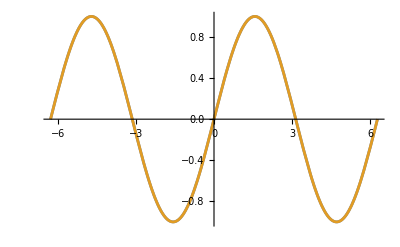

```mathematica
Plot[{Sin[x],approx[approx[x]]}, {x, -2Pi, 2Pi}]
```

#### Results for Taylor Series

We can use this code to generate approximations for other functions as well. For example, here is an approximation found for the function f(x)=1+x^2 by means of a taylor series:

```mathematica
(* Helper Functions *)
TaylorApprox[coefs_][x_]:=Sum[coefs[[i+1]]*x^i/Factorial[i], {i, 0, Length[coefs]-1}]
IntegralLoss[f_]:=NIntegrate[((1+x^2)-f[f[x]])^2, {x, -1,1}]

(* Outputted Coefficients *)
coefs=;

(* Final Approximation *)
approx=TaylorApprox[coefs];
```

While not as perfect as for sin, this process still yields a small error value, especially when considering that this function was often not handled well by other approximation algorithms:

```mathematica
IntegralLoss[approx]
```

0.0000408767

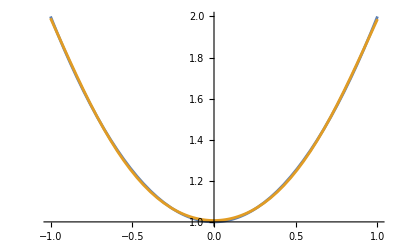

```mathematica
Plot[{1+x^2,approx[approx[x]]}, {x, -1, 1}]
```

#### Generalizability

Although one can fine-tune the optimizations for better results, or choose between taylor series, fourier series, and linear spline approximations, here are the loss values for a variety of functions all trained with the same parameters over the range [-1, 1]:

f(x) = x^2 + 1 | 0.000111133

f(x) = 2x + 3 |  2.94388*10^-6

f(x) = cos(x) | 0.0189814

f(x) = e^x | 0.000010337

f(x) = ln(2 + x) | 0.0000279523

f(x) = {x < 0: x + 1, x^2} | 0.0768464

Although some functions achieve a much better result than others, this shows that there does generally exist a functional square root for many functions, and the existence of solutions (especially one over a fixed range), is not limited to a select few functions.

For comparison with the previous two examples, we should ideally test with the same range of [-2 Pi, 2 Pi]. However, every method of approximation I use with the genetic algorithm seems to diverge, getting quite poor results (worse than the previous method by a couple orders of magnitude). Because of this, I’ve included both values:

f(x) = Sin(x) + Sigmoid(x) where -1 < x < 1 | 8.05862*10^-7

f(x) = Sin(x) + SIgmoid(x) where -2 Pi < x < 2 Pi | 0.433118

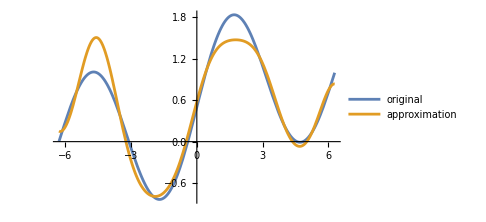

## Conclusion

## Results

Throughout this paper, we discussed a formal definition for non-integer functional iteration, and presented both formulaic solutions for specific functions as well as numerical techniques for finding fairly accurate approximations of functional roots. Most of our formulas were able to be generalized to complex iteration of complex functions, which implies that it is often possible to extend iteration to complex functions and complex exponents.

Our numerical techniques were able to find solutions for a much greater variety of functions, and showed that there were a large number of methods to compute functional iterates. Overall, the most accurate and extensible method was optimization of the coefficients of a taylor series by means of a genetic algorithm. However, this method was also somewhat limited in the domain due to divergence outside of the interval (-1, 1) (as high-degree terms tend to dominate outside of that range). Other function-approximating series may be better suited for this, but within that interval, taylor series seem to work quite well.

## Future Work

For formulaic solutions, we mostly used solutions in terms of arithmetic operations. However, using infinite sums or integrals may allow one to apply our techniques for solving functional iteration to a wider variety of function types. In particular, solving for a half iterate by means of a fourier series may be possible for many more functions, especially periodic functions. Promisingly, Newton Series can often be used to solve this type of problem, as is used in https://mathoverflow.net/questions/17605/how-to-solve-ffx-cosx/44727#44727.

As for numerical approximations, although we found a variety of methods, the ones which yielded the best results relied heavily on random search and generalized function approximation (instead of iterate-specific improvements). This implies that more efficient algorithms such as gradient descent, simulated annealing, etc. may converge much more quickly on solutions. A more

## Acknowledgements

Lastly, we’d like to thank a couple people who made our WELP project possible. Many thanks to Eryn Gillam and Rory Foulger, who make this program possible. We’d also like to thank our mentor Daniele Ceravolo for everything he helped us with along the way. Finally, thanks to every YouTube Video, textbook, and teacher who gave us the math and the computer skills necessary to get here.